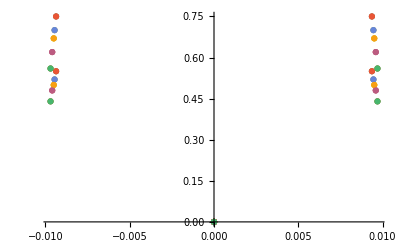

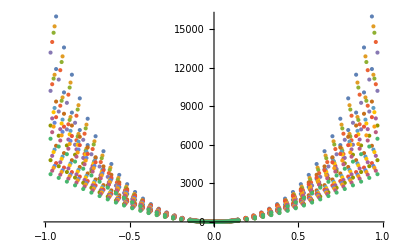

```mathematica
m={12.0107,91.224,1};kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;
(*Data in*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
filesC={"C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZr={"Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};
filesCh={"1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805","1.harm.C_4685_760_110","1.harm.C_4730_1900_110","1.harm.C_4759_2500_110","1.harm.C_4801_3200_110","1.harm.C_4850_3805_110","1.harm.C_4685_760_111","1.harm.C_4730_1900_111","1.harm.C_4759_2500_111","1.harm.C_4801_3200_111","1.harm.C_4850_3805_111"};
filesZrh={"1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805","1.harm.Zr_4685_760_110","1.harm.Zr_4730_1900_110","1.harm.Zr_4759_2500_110","1.harm.Zr_4801_3200_110","1.harm.Zr_4850_3805_110","1.harm.Zr_4685_760_111","1.harm.Zr_4730_1900_111","1.harm.Zr_4759_2500_111","1.harm.Zr_4801_3200_111","1.harm.Zr_4850_3805_111"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,15}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,15}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,15}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,15}];
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

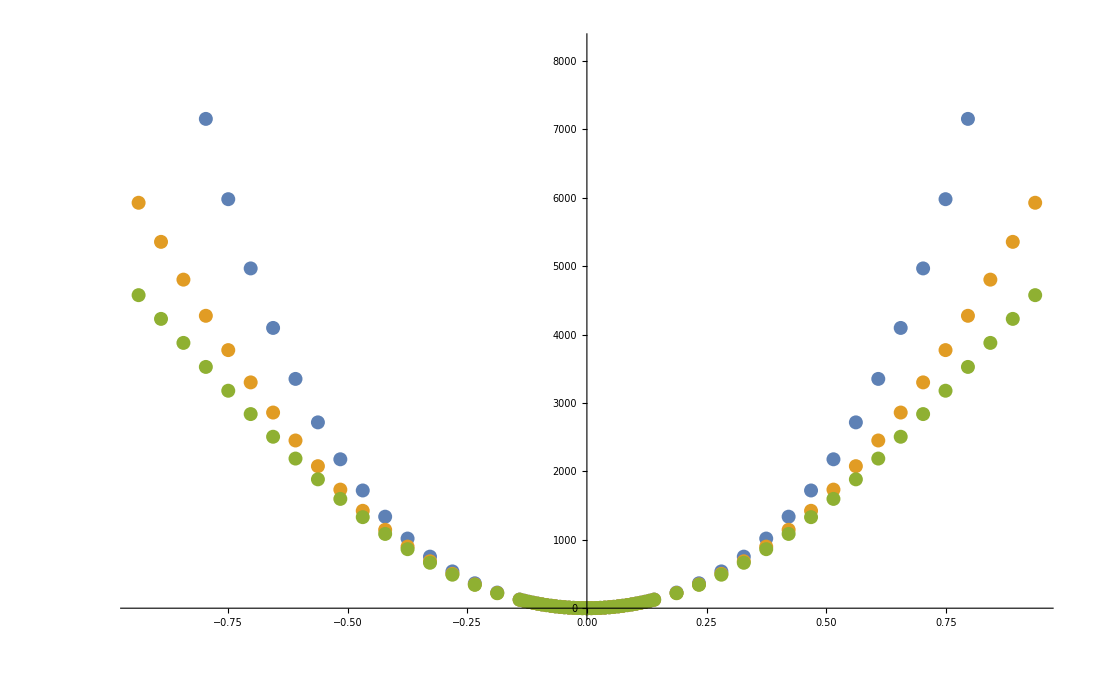

```mathematica
ListPlot[{Cdata[[1]],Cdata[[6]],Cdata[[11]],hCdata}]
```

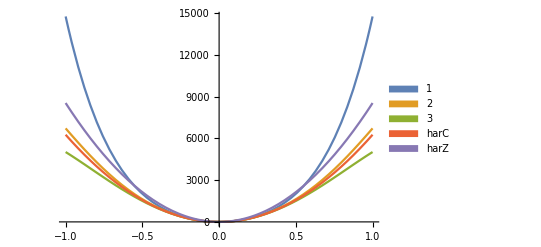

```mathematica
Plot[Evaluate@{V[1,6,x],V[1,2,x][[1]],V[2,2,x][[1]]},{x,-1,1},PlotLegends->SwatchLegend[{1,2,3,harC,harZ}]]
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,15}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,15,5}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,15,5}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15,5}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15,5}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]

V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,15}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,15,5}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,15,5}]
V[2,8,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,15,5}]
V[2,10,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,15,5}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,15}]
GraphicsGrid[{{Show[Plot[Evaluate@{V[1,2,x][[1]],V[1,12,x][[1]],V[1,12,x][[6]],V[1,12,x][[11]]},{x,-1.2,1.2},PlotLegends->SwatchLegend[{"harmonic","100 anharmonic","110 anharmonic","111 anharmonic"}],PlotLabel->"Carbon potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],ImageSize->500],Show[Plot[Evaluate@{V[2,2,x][[1]],V[2,12,x][[1]],V[2,12,x][[6]],V[2,12,x][[11]]},{x,-1.2,1.2},PlotLegends->SwatchLegend[{"harmonic","100 anharmonic","110 anharmonic","111 anharmonic"}],PlotLabel->"Zirconium potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],ImageSize->500]}},ImageSize->1300]
```

-Graphics-

```mathematica
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,1}]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,1}]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{6264.46}

cOmega0 in meV/Ang**2/AMU is approximately

{32.2978}

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{8542.44}

Z_Omega_0 in meV/Ang**2/AMU is approximately

{13.6852}

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=350;
(*Define bounds for plotting and solving eigenproblem*)
B=1.2;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒallc=Table[-(1/(2m[[1]]))*u''[x]+V[1,i,x]*u[x],{i,2,12,10}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,i,x]*u[x],{i,2,12,10}];
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}};
```

```mathematica
(*ℒallc[[1=harmonic]]ℒallc[[2=anharmonic 12th order]]*)
ℒallc;
```

```mathematica
char1d=Table[NDEigensystem[ℒallc[[1]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,15}];
canh1d=Table[NDEigensystem[ℒallc[[2]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,15}];
```

```mathematica
zhar1d=Table[NDEigensystem[ℒallz[[1]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,15}];
zanh1d=Table[NDEigensystem[ℒallz[[2]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,15}];
```

```mathematica
maxval=250;
char1de=Table[char1d[[i]][[1]][[1;;maxval]],{i,1,15}];
canh1de=Table[canh1d[[i]][[1]][[1;;maxval]],{i,1,15}];
zhar1de=Table[zhar1d[[i]][[1]][[1;;maxval]],{i,1,15}];
zanh1de=Table[zanh1d[[i]][[1]][[1;;maxval]],{i,1,15}];
```

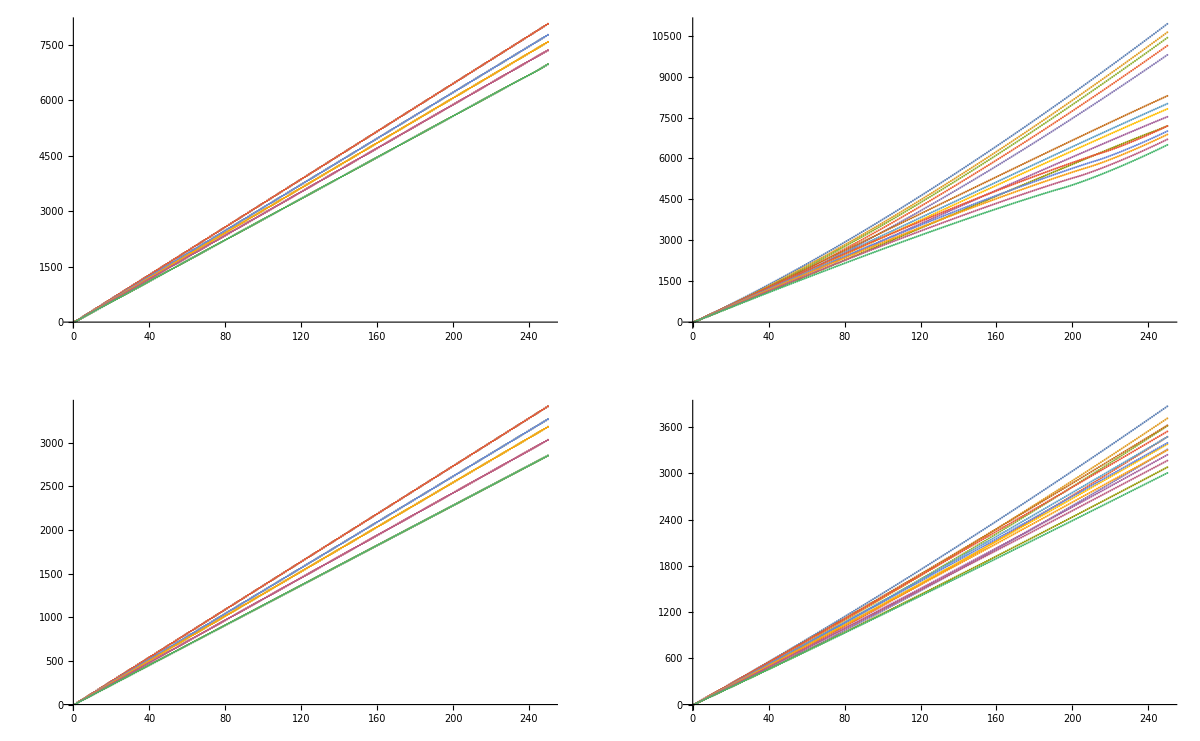

```mathematica
GraphicsGrid[{{ListPlot[char1de],ListPlot[canh1de[[1;;15]]]},{ListPlot[zhar1de],ListPlot[zanh1de[[1;;15]]]}},ImageSize->1200]
```

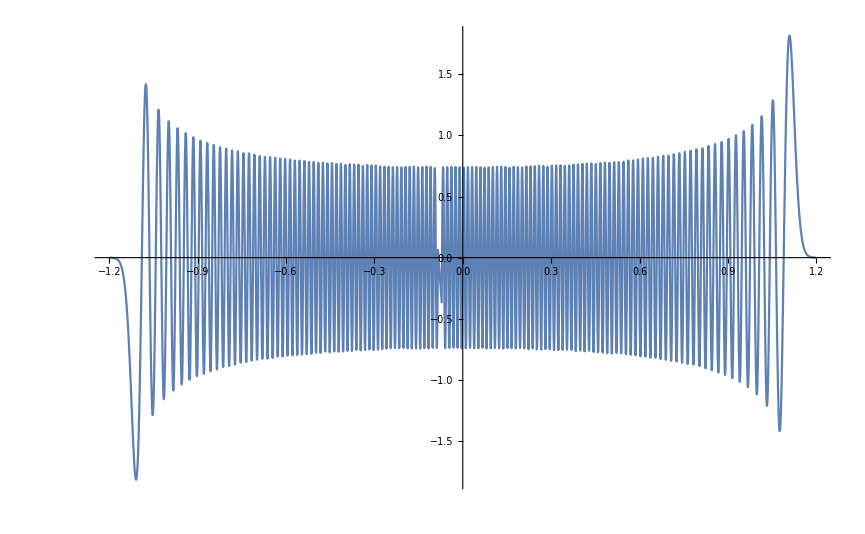

```mathematica
Plot[canh1d[[2]][[2]][[2]][[250]],{x,-1.2,1.2}]
```

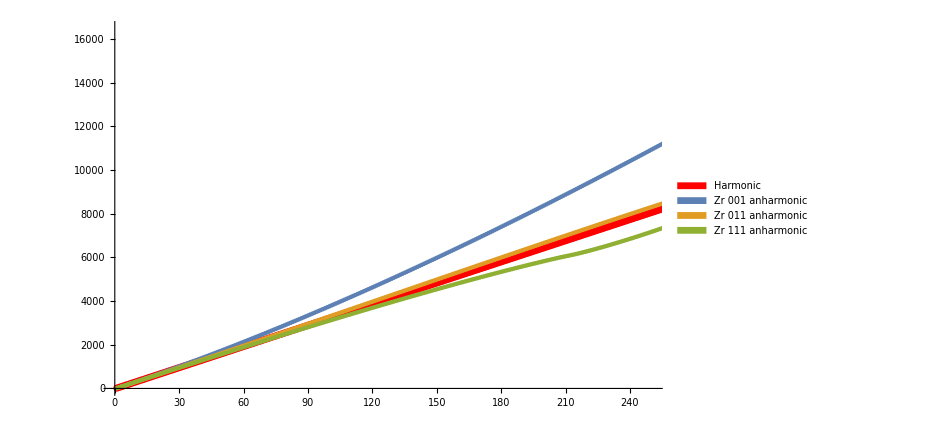

```mathematica
(*Repeated of above WITH 400 EIGENVALUES*)
(*Table[2*16.148887026360963(i+0.5),{i,0,300,1}]*)
Show[ListPlot[char1d[[2]][[1]],PlotStyle->{Red},PlotLegends->SwatchLegend[{"Harmonic"}],ImageSize->700],ListPlot[Table[canh1d[[i]][[2]][[1]],{i,1,3}],PlotLegends->SwatchLegend[{"Zr 001 anharmonic","Zr 011 anharmonic","Zr 111 anharmonic"}]],PlotRange->{{0,250},Automatic}]
```

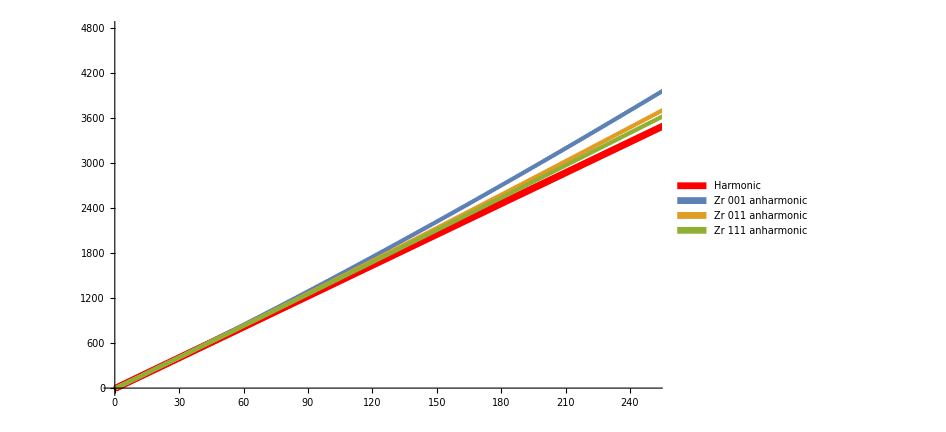

```mathematica
Show[ListPlot[zhar1d[[2]][[1]],PlotStyle->Red,PlotLegends->SwatchLegend[{"Harmonic"}],PlotRange->{{0,250},Automatic},ImageSize->700],ListPlot[Table[zanh1d[[i]][[2]][[1]],{i,1,3}],PlotLegends->SwatchLegend[{"Zr 001 anharmonic","Zr 011 anharmonic","Zr 111 anharmonic"}]]]
```